# 22 Gaussian Elimination: Stability

## Pivoted LU

Here is our Pivoted LU Code

```mathematica
Clear[LUTogetherPivoted]
LUTogetherPivoted[A_]:=Module[{m=Length[A],LU=A, p, col ,i},
p=Range[m]; 
Do[
(* Find Max Position *)
col=Abs[LU⟦All,k⟧]; col⟦1;;k-1⟧*=0;
i=FirstPosition[col,Max[col]]⟦1⟧;
(* Switch Rows Book Keeping *)
p⟦{k,i}⟧=p⟦{i,k}⟧;
(* Switch Rows *)
LU⟦{k,i}⟧=LU⟦{i,k}⟧;
Do[
LU⟦j,k⟧=LU⟦j,k⟧/LU⟦k,k⟧;
(* Diagonals store U not L. Index range excludes the diagonal. *)
LU⟦j,k+1;;m⟧-=LU⟦j,k⟧ LU⟦k,k+1;;m⟧,
{j,k+1,m}],
{k,1,m-1}];
(* Splitting LU to maintain the return values *)
{LowerTriangularize[LU,-1]+IdentityMatrix[m],UpperTriangularize[LU],p}
]
```

As always test!

```mathematica
m=123;A=RandomReal[{-1,1},{m,m}];
{L,U,p}=LUTogetherPivoted[A];
Norm[A⟦p⟧-L.U]
TabView[{
"L"->MatrixPlot[L,PlotLegends->Automatic],
"U"->MatrixPlot[U,PlotLegends->Automatic]}]
```

1.90908×10^-14

12

Pivoting has made sure |L_(i,j)|≤1 for all i and j. On the other hand the U values can (and do) get larger. A common measure of how bad a matrix is for partial pivoting is how big the U entries get!

### Growth Factor

The the LU decomposition growth factor for A=L.U is 
	ρ=(max_(i,j) |U_ij|)/(max_(i,j) |A_(i,j)|)
It looks like for random matrices ρ is usually not that big

{0.3125,Null}

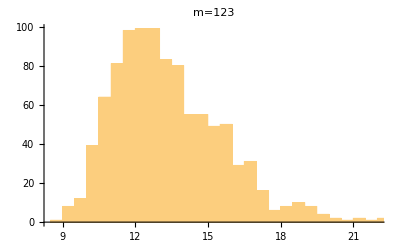

```mathematica
SampleSize=10^3;
m=123;
Timing[GrowthFactors=Table[
A=RandomReal[{-1,1},{m,m}];
{LU,p,c}=LUDecomposition[A];
Max[Abs[LU]]/Max[Abs[A]],{SampleSize}];]
Histogram[GrowthFactors,40,
PlotLabel->StringForm["m=``",m]]
```

## Worst Case Growth Factor

Row pivoting works for almost all randomly generated matrices and is very widely used in practice. To see that bad behavior is possible lets try to row reduce the following artificial example.

```mathematica
m=6;
BadMat= LowerTriangularize[ConstantArray[-1,{m,m}],-1]+IdentityMatrix[m];
BadMat⟦All,m⟧=ConstantArray[1,m];
MatrixForm[BadMat]
```

(1 | 0 | 0 | 0 | 0 | 1
-1 | 1 | 0 | 0 | 0 | 1
-1 | -1 | 1 | 0 | 0 | 1
-1 | -1 | -1 | 1 | 0 | 1
-1 | -1 | -1 | -1 | 1 | 1
-1 | -1 | -1 | -1 | -1 | 1)

```mathematica
Clear[A,m]
m=12;
BadMat= LowerTriangularize[ConstantArray[-1,{m,m}],-1]+IdentityMatrix[m];
BadMat⟦All,m⟧=ConstantArray[1,m];
A[0]=BadMat;
A[k_]:=A[k]=Module[{M=A[k-1]}, 
m= Length[M];Do[M⟦i⟧+=M⟦k⟧,{i,k+1,m}];
M]
TabView[Map[MatrixForm,Map[A,Range[m]-1]]]
```

123456789101112

```mathematica
2.^54
```

1.80144×10^16

So row reduction with row pivoting can certainly produce large values! This is in fact the worst possible growth factor of 2^(m-1)! Technically row pivoting makes an LU Decomposition backward stable.  However, the worst possible case constant is 2^(m-1) which is big enough to make that conclusion silly!

## Practical Considerations

In real world matrices growth factors are well behaved and partial pivoting is widely used for dense matrices that fit in computer memory.

### Storing and Using an LU Decomposition

Most of the work in solving a linear system is in the LU decomposition!  It is not uncommon to need to solve several systems with the same right hand side. If you need to do this you should save and recycle the LU Decomposition.

In Mathematica this looks like this with timings attached.

```mathematica
m=10^4;
A=RandomReal[{-1,1},{m,m}];
{b1,b2,b3,b4}=RandomReal[{-1,1},{4,m}];
Timing[ LSolFun=LinearSolve[A];]
Timing[ LSolFun[b1];LSolFun[b2];LSolFun[b3];LSolFun[b4];]
Timing[ LinearSolve[A,b1];]
```

{5.6875,Null}

{0.21875,Null}

{5.625,Null}